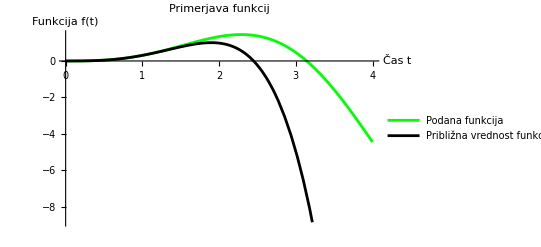

```mathematica
f[t_]:=Sin[t]*t^2*Exp[-1]

Taylor=Series[f[t],{t,0,5}];

približek=Normal[Taylor];



Plot[Evaluate[{f[t],približek}],{t,0,4},PlotStyle->{Directive[Green],Directive[Black]},

PlotLegends->{"Podana funkcija","Približna vrednost funkcije (Taylor)"},AxesLabel->{"Čas t","Funkcija f(t)"},PlotLabel->"Primerjava funkcij"]
```